```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

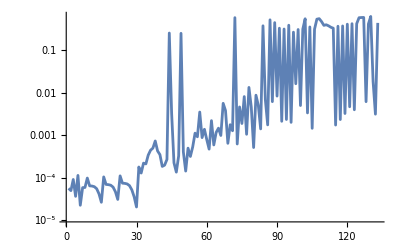

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-19.3776,L2PhaseSet→-39.2702,Q1EkG→155.762,Q2EkG→-160.329,Q3EkG→110.087,Q4EkG→131.41,Q5EkG→-23.8163,Q6EkG→-145.897,PDrive_mean_x→-3.4575×10^-6,PDrive_mean_y→7.372×10^-7,PDrive_sigma_x→0.0000558027,PDrive_sigma_y→0.0000494713,PDrive_mean_xp→0.0000215689,PDrive_mean_yp→1.0196×10^-6,PDrive_xCost→0.0000559097,PDrive_yCost→0.0000494768,PDrive_totalCost→0.0000526932,PDrive_emitSI90_x→0.0000928551,PDrive_emitSI90_y→6.625×10^-6,PDrive_zLen→0.0000298699,PDrive_zCentroid→991.332,PWitness_mean_x→-0.0000843902,PWitness_mean_y→-2.173×10^-6,PWitness_sigma_x→0.0000605937,PWitness_sigma_y→0.0000307269,PWitness_mean_xp→-0.000154927,PWitness_mean_yp→-3.2127×10^-6,PWitness_xCost→0.000103891,PWitness_yCost→0.0000308036,PWitness_totalCost→0.0000673472,PWitness_emitSI90_x→0.0000393651,PWitness_emitSI90_y→6.3345×10^-6,PWitness_zLen→0.0000264124,PWitness_zCentroid→991.332,bunchSpacing→0.000278219,transverseCentroidOffset→0.000080985,maximizeMe→0.618477|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -19.3776053958
L2PhaseSet : -39.2701775428
Q1EkG : 155.7620522877
Q2EkG : -160.3289317715
Q3EkG : 110.0874217725
Q4EkG : 131.4102626571
Q5EkG : -23.8162720347
Q6EkG : -145.8974106485
PDrive_mean_x : -3.4575e-6
PDrive_mean_y : 7.372e-7
PDrive_sigma_x : 0.0000558027
PDrive_sigma_y : 0.0000494713
PDrive_mean_xp : 0.0000215689
PDrive_mean_yp : 1.0196e-6
PDrive_xCost : 0.0000559097
PDrive_yCost : 0.0000494768
PDrive_totalCost : 0.0000526932
PDrive_emitSI90_x : 0.0000928551
PDrive_emitSI90_y : 6.625e-6
PDrive_zLen : 0.0000298699
PDrive_zCentroid : 991.3316726126
PWitness_mean_x : -0.0000843902
PWitness_mean_y : -2.173e-6
PWitness_sigma_x : 0.0000605937
PWitness_sigma_y : 0.0000307269
PWitness_mean_xp : -0.0001549273
PWitness_mean_yp : -3.2127e-6
PWitness_xCost : 0.0001038908
PWitness_yCost : 0.0000308036
PWitness_totalCost : 0.0000673472
PWitness_emitSI90_x : 0.0000393651
PWitness_emitSI90_y : 6.3345e-6
PWitness_zLen : 0.0000264124
PWitness_zCentroid : 991.3319508314
bunchSpacing : 0.0002782188
transverseCentroidOffset : 0.000080985
maximizeMe : 0.6184768027

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

0.000080985

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv